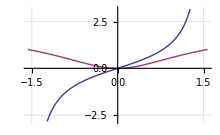

```mathematica
Plot[{Tan[x], ArcTan[x]^2},{x,-Pi/2, Pi/2}, GridLines->Automatic, GridLinesStyle->LightGray]
```

```mathematica
Table[i, {i,10,15}]
```

{10,11,12,13,14,15}

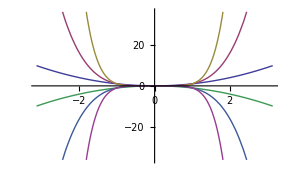

```mathematica
Plot[{a^2, a^4, a^6, -a^2, -a^4, -a^6}, {a, -Pi, Pi}]
```

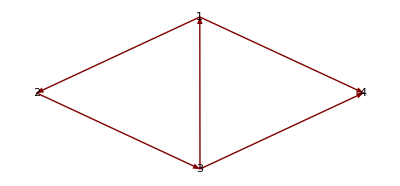

```mathematica
GraphPlot[{1->2,2->3,3->1,3->4,1->4},DirectedEdges->True,
VertexLabeling->True]
```

```mathematica
Array[f,11]
```

{f[1],f[2],f[3],f[4],f[5],f[6],f[7],f[8],f[9],f[10],f[11]}

```mathematica
myRange=Range[1,14,2]
```

{1,3,5,7,9,11,13}

```mathematica
myRange^2
```

{1,9,25,49,81,121,169}

```mathematica
Total[myRange]
```

49

```mathematica
Length[myRange]
```

7

```mathematica
(*Dette er Dot produkt:*)
{1,2,3}.{2,3,4}
```

20

```mathematica
Dimensions[myRange]
```

{7}

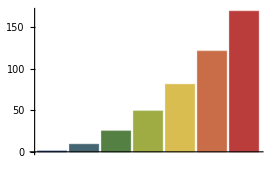

```mathematica
BarChart[myRange^2, ChartStyle->"DarkRainbow"]
```

```mathematica
p = 1;
For [i = 0, i < 10, i++; p = p + 2]
```

```mathematica
p
```

21

```mathematica
BitOr[256, 127]
```

383

```mathematica
BitAnd[123, 190]
```

58

```mathematica
BitXor[1, 2]
```

3

```mathematica
BitShiftLeft[1, 8]
```

256

```mathematica
BitShiftRight[256, 4]
```

16

```mathematica
IntegerDigits[255, 2] (* Show bits *)
```

{1,1,1,1,1,1,1,1}

```mathematica
BitGet[128, 7]
```

1

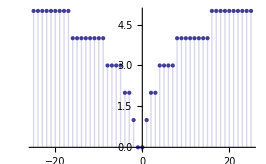

```mathematica
DiscretePlot[BitLength[n],{n,-25,25}]
```

```mathematica
2  > 1 && Pi < 3
```

False

```mathematica
2≠2
```

False

```mathematica
{BitOr[5, 7], BitAnd[5, 7], BitXor[5, 7]}
```

{7,5,2}

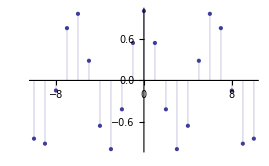

```mathematica
DiscretePlot[Cos[n],{n,-10,10}]
```

```mathematica
Table[i^2,{i,10}]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
myTable = Table[10i+j,{i,4},{j,3}]
```

{{11,12,13},{21,22,23},{31,32,33},{41,42,43}}

```mathematica
MatrixForm[myTable]
```

(11 | 12 | 13
21 | 22 | 23
31 | 32 | 33
41 | 42 | 43)

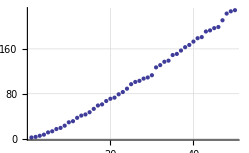

```mathematica
ListPlot[Table[Prime[i],{i,50}], GridLines->Automatic,
GridLinesStyle->LightGray]
```

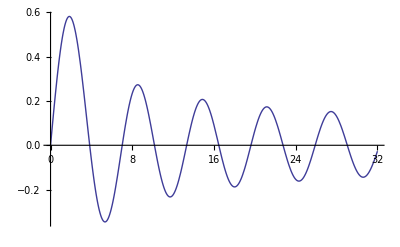
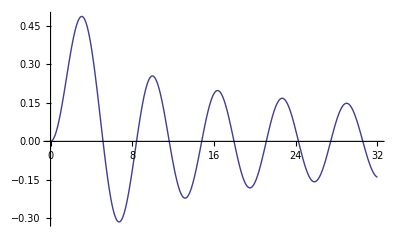
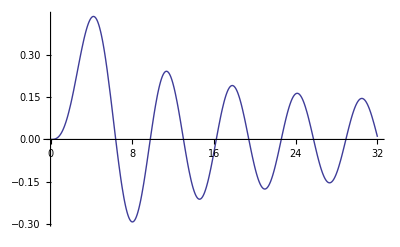

```mathematica
Table[Plot[BesselJ[n,x],{x,0,32}],{n,3}]
```

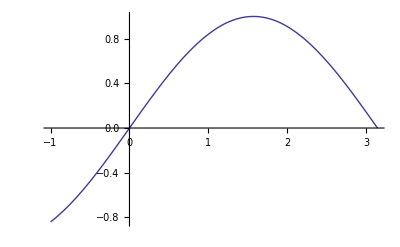
{-Graphics-,-Graphics-}

```mathematica
Table[Plot[Sin[x] , {x, -1,  Pi}], {y, 2}]
```

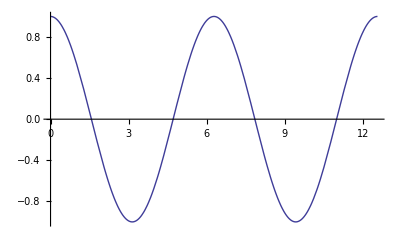
{-Graphics-,-Graphics-}

```mathematica
Table[Plot[Cos[x] , {x, 0, 4 * Pi}],{y, 2}]
```

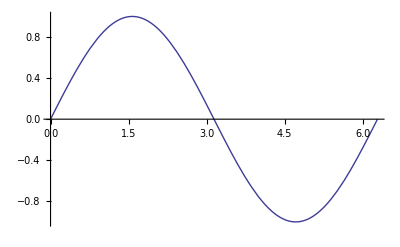

```mathematica
Table[Plot[Sin[x] , {x, 0, 2 * Pi}], {y, 1}]
```

```mathematica
Manipulate[Plot[{Sin[x+a], Cos[x + a], -Sin[x+a], -Cos[x+a]} ,
{x, 0, 2Pi}, Filling->Axis], {a, 0, 20}]
```

```mathematica
Manipulate[Plot[Cos[x^a], {x, 0, 2 * Pi}], {a, 0, 40}]
```

```mathematica
(* Define a function: *)
MyFunc:= (2 * 2 *2)
```

```mathematica
MyFunc * MyFunc
```

64

```mathematica
(* Space = Multiplication: *)
(MyFunc MyFunc) / 2
```

32

```mathematica
a=5
```

5

```mathematica
(* Ctrl+, -> Insert new row vector: *)
({{a, b, c, d, e, f}})
```

{{5,b,c,d,e,f}}

```mathematica
(* Ctrl+Enter -> Insert new column vector: *)
({{a}, {b}, {c}, {d}, {e}})
```

{{5},{b},{c},{d},{e}}

```mathematica
x1 = Array["stuff", 4]
```

{stuff[1],stuff[2],stuff[3],stuff[4]}

```mathematica
y1 = x1*2
```

{2 stuff[1],2 stuff[2],2 stuff[3],2 stuff[4]}

```mathematica
x2 = Range[1.0, 2.0, 0.1] (* Increment by 0.1 *)
```

{1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.}

```mathematica
x2 x2 (* Multiplication *)
```

{1.,1.21,1.44,1.69,1.96,2.25,2.56,2.89,3.24,3.61,4.}

```mathematica
theMedian = Mean[x2];
```

```mathematica
theMedian / 2
```

0.75

```mathematica
(* Testing if-statements *)
myTestNumber = 56;
If[myTestNumber < 56, "Less than 56", "Greater than 56"]
```

Greater than 56

```mathematica
(* Define function name with functionName := [Body...] *)
myWhileFunction:=
While[myTestNumber > 50,
myTestNumber--;
If[myTestNumber < 54, Print["Number is: ", myTestNumber, "...!"]];
]
```

```mathematica
myWhileFunction (* Call the function! *)
```

Number is: 53...!

Number is: 52...!

Number is: 51...!

Number is: 50...!